# Study of the Klein-Gordon equation

Prof. Dr. Rafael Poliseli Teles

Departamento de física, IGCE, UNESP, Brazil

## Introducton

The Klein-Gordon equation describes relativistic spinless particles as pions (π-mesons), which a scalar field represents π^0 (non-charged π-meson) and a complex field represents π^+ and π^- (charged π-mesons).

Deduction Klein-Gordon equation
E^2=p^2 c^2+m^2 c^4
Ê→i ℏ ∂_t and p̂→-i ℏ∇
-1/c^2∂_t^2 Φ+∇^2 Φ=(m^2 c^2)/ℏ^2 Φ
Natural units: ℏ=c=1
-∂_t^2 Φ+∇^2 Φ=m^2 Φ
Deduction of continuity equation

## Stationary solutions of Klein-Gordon equation

Proposing a plane wave solution Φ(r,t)=ⅇ^(ⅈ (k·r-ω t)).

```mathematica
Φ[x_,y_,z_,t_]:=ⅇ^(-ⅈ ω t)*ⅇ^(ⅈ (kx*x+ky*y+kz*z))

-D[Φ[x,y,z,t],t,t]+D[Φ[x,y,z,t],x,x]+D[Φ[x,y,z,t],y,y]+D[Φ[x,y,z,t],z,z]==m^2 Φ[x,y,z,t]//FullSimplify
```

ⅇ^(ⅈ (kx x+ky y+kz z-t ω)) (kx^2+ky^2+kz^2+m^2-ω^2)==0

Dispersion relation ω^2=k^2+m^2
ω=±√(k^2+m^2) ++

## 1D solitary wave

### Free particle

```mathematica
ϕ1D[x_,t_]:=ϕ1D[x] ⅇ^(- ⅈ ω t)
DSolve[-D[ϕ1D[x,t],t,t]+D[ϕ1D[x,t],x,x]==m^2 ϕ1D[x,t],ϕ1D[x],x]
ClearAll@ϕ1D
```

{{ϕ1D[x]→ⅇ^(x √(m^2-ω^2)) C[1]+ⅇ^(-x √(m^2-ω^2)) C[2]}}

```mathematica
ϕ1D[x_,t_]:=ϕ1D[x] ⅇ^(ⅈ ω t)
DSolve[-D[ϕ1D[x,t],t,t]+D[ϕ1D[x,t],x,x]==m^2 ϕ1D[x,t],ϕ1D[x],x]
ClearAll@ϕ1D
```

{{ϕ1D[x]→ⅇ^(x √(m^2-ω^2)) C[1]+ⅇ^(-x √(m^2-ω^2)) C[2]}}

### Particle in a box potential

### Transmision through a potential barrier

## 1D gaussian wave packet

## Time-dependent variational method for each solution of Klein-Gordon equation

Lagrangians and variational method explanation.
ℒ=((∂ϕ)/(∂t))((∂ϕ^*)/(∂t))-(∇ϕ)(∇ϕ^*)-m^2 ϕ^*ϕ

## 1D solitary wave

The varational method is applied to the solution of 1D solitary wave from part about stationary solutions.
In order to solve the integrals it is necessary to use either periodic boundary conditions or a cutoff, since the system describes an free particle.

### c1(t) and c2(t) with periodic boundary conditions

The periodic boundary condition is given by ϕ(x-L)=ϕ(x+L). Since ϕ(x)=c_1 ⅇ^(ⅈ k x)+c_2 ⅇ^(-ⅈ k x),
ϕ(x-L)=ϕ(x+L)
c_1 ⅇ^(ⅈ k x-ⅈ k L)+c_2 ⅇ^(-ⅈ k x+ⅈ k L)=c_1 ⅇ^(ⅈ k x+ⅈ k L)+c_2 ⅇ^(-ⅈ k x-ⅈ k L)
(c_1 ⅇ^(ⅈ k x)-c_2 ⅇ^(-ⅈ k x))ⅇ^(-ⅈ k L)=(c_1 ⅇ^(ⅈ k x)-c_2 ⅇ^(-ⅈ k x))ⅇ^(ⅈ k L)
ⅇ^(2ⅈ k L)=1
we have k_n=(2π n)/L with n=1,2,3,4,5...

C[1]∈Integers&&((L≠0&&(k==-(ⅈ (ⅈ π+2 ⅈ π C[1]))/L||k==(2 π C[1])/L))||L==0)

{0,0,0,0,0}

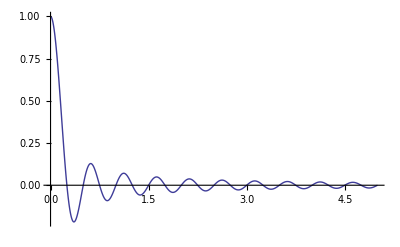

```mathematica
Reduce[ⅇ^(2ⅈ k L)==1,k]
Sin[4n π]/(4n π)/.n->{1,2,3,4,5}
Plot[Sin[4n π]/(4n π),{n,0,5},PlotRange->All]
```

```mathematica
ϕ1[x_,t_]:=(c1[t] ⅇ^(ⅈ (2π n)/L x)+c2[t] ⅇ^(-ⅈ (2π n)/L x))ⅇ^(-ⅈ ω t)
ϕ2[x_,t_]:=(c1[t] ⅇ^(-ⅈ (2π n)/L x)+c2[t] ⅇ^(ⅈ (2π n)/L x))ⅇ^(ⅈ ω t)
(*do a cutoff based on uncertain priciple, or divide the system into periodic conditions*)
L1=Integrate[D[ϕ1[x,t],t]*D[ϕ2[x,t],t],{x,-L,L}];
L2=-Integrate[D[ϕ1[x,t],x]*D[ϕ2[x,t],x],{x,-L,L}];
L3=-m^2 Integrate[ϕ1[x,t]*ϕ2[x,t],{x,-L,L}];
Lt=L1+L2+L3;
ClearAll[ϕ1,ϕ2,L1,L2,L3]
```

```mathematica
D[D[Lt,c1'[t]],t]
D[Lt,c1[t]]
D[D[Lt,c2'[t]],t]
D[Lt,c2[t]]
ClearAll@Lt
```

(L (4 n π c1''[t]+Sin[4 n π] c2''[t]))/(n π)

-(4 n π (4 n π c1[t]-c2[t] Sin[4 n π]))/L-L m^2 (4 c1[t]+(c2[t] Sin[4 n π])/(n π))+(L (4 n π ω^2 c1[t]+ω^2 c2[t] Sin[4 n π]))/(n π)

(L (Sin[4 n π] c1''[t]+4 n π c2''[t]))/(n π)

-(4 n π (4 n π c2[t]-c1[t] Sin[4 n π]))/L-L m^2 (4 c2[t]+(c1[t] Sin[4 n π])/(n π))+(L (4 n π ω^2 c2[t]+ω^2 c1[t] Sin[4 n π]))/(n π)

The equations of motions are given by: 
c_1^(..)+Sin[4 n π]/(4n π)c_2^(..)= (ω^2-m^2-(4 n^2 π^2)/L^2) c_1+(ω^2-m^2+(4 n^2 π^2)/L^2)Sin[4 n π]/(4n π)c_2 (1)
Sin[4 n π]/(4n π)c_1^(..)+c_2^(..)= (ω^2-m^2+(4 n^2 π^2)/L^2)Sin[4 n π]/(4n π)c_1+(ω^2-m^2-(4 n^2 π^2)/L^2) c_2 (2)
On the boundaries, Sin[4 n π]/(4 n π)=0 for n=1,2,3,4,5...
c_1^(..)=(ω^2-m^2-(4 n^2 π^2)/L^2) c_1 (3)
c_2^(..)=(ω^2-m^2-(4 n^2 π^2)/L^2) c_2 (4)
Between the boundaries for L→∞,
c_1^(..)+Sin[4 n π]/(4n π)c_2^(..)=(ω^2-m^2) c_1+(ω^2-m^2)Sin[4 n π]/(4n π)c_2 (5)
Sin[4 n π]/(4n π)c_1^(..)+c_2^(..)=(ω^2-m^2)Sin[4 n π]/(4n π)c_1+(ω^2-m^2) c_2 (6)

{{c1[t]→InterpolatingFunction[{{0.,100.}},<>][t],c2[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

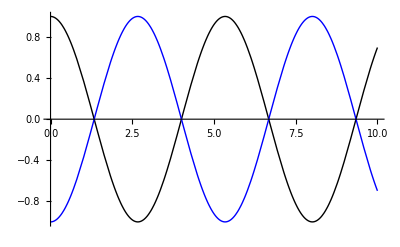

```mathematica
n=1;
L=10;
c10=1;
c20=-1;
m=1;
ω=0.1;
eq1=c1''[t]+(Sin[4 n π] c2''[t])/(4n π)==(ω^2-m^2-(4 n^2 π^2)/L^2) c1[t]+(ω^2-m^2+(4 n^2 π^2)/L^2)(c2[t] Sin[4 n π])/(4n π);
eq2=c2''[t]+(Sin[4 n π] c1''[t])/(4n π)==(ω^2-m^2-(4 n^2 π^2)/L^2) c2[t]+(ω^2-m^2+(4 n^2 π^2)/L^2)(c1[t] Sin[4 n π])/(4n π);
solution=NDSolve[{eq1,eq2,c1[0]==c10,c2[0]==c20,c1'[0]==0,c2'[0]==0},{c1[t],c2[t]},{t,0,100}]
Plot[{c1[t]/.solution,c2[t]/.solution},{t,0,10},PlotStyle->{Black,Blue}]
ClearAll[c10,c20,n,L,solution,m,ω,eq1,eq2]
```

### k(t), c1(t) and c2(t) with boundary conditions

```mathematica
ϕ1[x_,t_]:=c1[t] ⅇ^(ⅈ k[t]x)+c2[t] ⅇ^(-ⅈ k[t]x)
ϕ2[x_,t_]:=c1[t] ⅇ^(-ⅈ k[t]x)+c2[t] ⅇ^(ⅈ k[t]x)
Integrate[D[ϕ1[x,t],t]*D[ϕ2[x,t],t],{x,-L,L}]
Integrate[D[ϕ1[x,t],x]*D[ϕ2[x,t],x],{x,-L,L}]
Integrate[ϕ1[x,t]*ϕ2[x,t],{x,-L,L}]
ClearAll[ϕ1,ϕ2]
```

1/(3 k[t]^3)(6 k[t]^2 (Sin[2 L k[t]] c1'[t] c2'[t]+L k[t] (c1'[t]^2+c2'[t]^2))+3 k[t] (2 L Cos[2 L k[t]] k[t]-Sin[2 L k[t]]) (c2[t] c1'[t]+c1[t] c2'[t]) k'[t]+(-6 L c1[t] c2[t] Cos[2 L k[t]] k[t]+2 L^3 (c1[t]^2+c2[t]^2) k[t]^3+3 c1[t] c2[t] (1-2 L^2 k[t]^2) Sin[2 L k[t]]) k'[t]^2)

2 k[t] (L (c1[t]^2+c2[t]^2) k[t]-c1[t] c2[t] Sin[2 L k[t]])

2 (L c1[t]^2+L c2[t]^2+(c1[t] c2[t] Sin[2 L k[t]])/k[t])